# Constrained method

## Start

```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->Automatic]
```

```mathematica
packageDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"pyramid1d`"
<<"pyramidalCyclope1D`"
```

```mathematica
noteBookMode="ConstrainedNewMethod";
```

## Test Points {line1, line2, pyrf12}

```mathematica
(* We create test points for compilation test *)
line1=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1,30}],1];
line2=GaussianFilter[Table[If[11<= p<=18,1,0],{p,1-1,30-1}],1];
ListPlot[{line1, line2},Joined->True,PlotMarkers->Automatic,PlotRange->All,PlotLabel->"Test Points",PlotLegends->{"ia","ib"}];
```

```mathematica
(*generate functions of pyramid with pyrFuncGen*)
(* input-> {original points, number of levels}*)
(* Output-> {functions f and df for n+1 levels} *)
pyrf1=pyrFuncGen[line1,3];
pyrf2=pyrFuncGen[line2,3];
pyrf12=Flatten[{pyrf1, pyrf2}, {{2},{1},{3}}];

Plot[{pyrf12[[4,1,1]][x],pyrf12[[4,2,1]][x]},{x,1,30}];
```

## Pyramidal Flow 1D (PyrFlow1D)

### PyrUpgrade1D

```mathematica
(* Function to update values of v1 and v2 with Over Constrained standards *)
(* Any value that does not meets the constraints becomes 0 *)

(* Input-> {{initial values for v1, v2 and status, and counter e}, pixel of interest, {functions f1, df1, f2, df2}, threshold for magnitude error}*)
(* Output-> {new values for v1, v2 and status and e} *)
PyrUpgrade1D[{v1_,v2_,status_,e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedNewMethod"]:=Block[{fric1,fric2,p1, p2, c,d1,d2,dv1,dv2},(

p1=p0-v1;
p2=p0+v2;

c = (fline1[p0]+fline2[p0])/2;
d1=dfline1[p1];
d2=dfline2[p2];

fric1=0.5*dfline1'[p1];
fric2=0.5*dfline2'[p2];

(* d1 and d2 have to be the same sign in every iteration *)
If[d1*d2 <0, If[e<2,Return[{v1,v2,"sign",e+1}],Return[{0.,0.,"sign",e}]]];

(* Change of sign during iteration *)
If[(Abs[d1]<threshold||Abs[d2]<threshold ),If[e<2,Return[{v1,v2,"mag",e+1}],Return[{0.,0.,"mag",e}]]];

(* Change of sign during iteration *)
(*If[(dfline1[p0]*d1<0||dfline2[p0]*d2<0),If[e<2,Return[{v1,v2,"flip",e+1}],Return[{0.,0.,"flip",e}]]];*)

(* dv1,dv2 : step from last {v1,v2} to new {v1,v2} *)
{dv1,dv2}= {(fline1[p1]-c)/(d1+Sign[d1]*Abs[fric1]),(c-fline2[p2])/(d2+Sign[d2]*Abs[fric2])};

{v1+dv1,v2+dv2,If[Norm[{dv1,dv2}]<0.001,"converged","ok"],e}

)];

(* No other solution will be calculated when status records an error message in this pyramidal level*)
(* status: "OK" -> solution respects constraints,  errors: "sign", "mag", "flip" *)
(* status: "converged" -> we converged!! *)

PyrUpgrade1D[{v1_,v2_,status_,2},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedNewMethod"]:=Return[{0,0,status,2}];

PyrUpgrade1D[{v1_,v2_,"sign",e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedNewMethod"]:=Return[{v1,v2,"sign",e}];

PyrUpgrade1D[{v1_,v2_,"mag",e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedNewMethod"]:=Return[{v1,v2,"mag",e}];

PyrUpgrade1D[{v1_,v2_,"flip",e_},p0_, {{fline1_,dfline1_} ,{fline2_,dfline2_}}, threshold_,"ConstrainedNewMethod"]:=Return[{v1,v2,"flip",e}];
```

### Test

```mathematica
(* initial values *)
{v1, v2,status,e}={0.,0.,"ok",0.};
i=0;
p=15;
```

```mathematica
n=2;
status="ok";
```

```mathematica
(*Test for PyrUpgrade1D, manual test to iterate multiple times*)
(* n is the level of pyramid *)

{v1,v2,status,e}=PyrUpgrade1D[{v1,v2,status,e},p, pyrf12[[n]],0.01,noteBookMode]
```

{0.,0.,sign,1.}

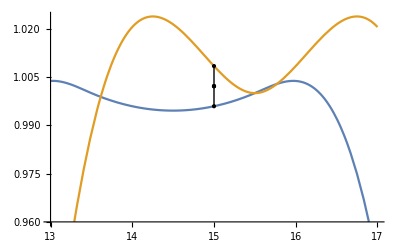

```mathematica
(* see *)
seePlot[p,2,{v1,v2},pyrf12[[n]]]
```

### PyrFlow1D

```mathematica
newValues[i_,{v1_,v2_}]:=Block[{},(
v=v1+v2;

Table[
r=RandomReal[];
rs={r,1-r}*v
,{j,i}]

)]
```

```mathematica
newValues[5,{3.5,0.6}]
```

{{1.91555,2.18445},{0.195176,3.90482},{1.22525,2.87475},{3.02032,1.07968},{0.981284,3.11872}}

```mathematica
pickNewValue[tableNewVals_]:=Block[{newVal},(

newVal=Select[tableNewVals,#[[3]]==("converged")&,1];

If[newVal=={},
tableNewVals[[1]],
newVal[[1]]]

)]
```

```mathematica
(* Function to find solutions for all levels of pyramid {l1,l2,l3,l4,...} or {l1} *)
(* Input-> {number of iterations, pixel of interests, pyrfunctions,threshold *)
(* Output-> {v1, v2,status}*)
PyrFlow1D[i_, p0_, pyrfunctions_,threshold_,"ConstrainedNewMethod"]:=Block[{v1, v2,c,status},(

c=Length[pyrfunctions]; (* number of levels *)

(*{v1, v2, status, e}*)
updateValues={0.,0.,"ok",0};

Do[

(* compute at this scale, using current motion estimate *)
If[updateValues[[4]]<2,updateValues[[3]]="ok", updateValues={0.,0.,updateValues[[3]],2}];

(* we get 5 new values *)
newVals=newValues[100,updateValues[[1;;2]]];

tableNewValues=Table[

updateValues[[1;;2]]=v;

Do[

updateValues=PyrUpgrade1D[updateValues,p0, pyrfunctions[[-f]],threshold*2^(-c+1),"ConstrainedNewMethod"]

,{j,1,i}];

updateValues
,{v,newVals}];

updateValues[[1;;2]]=pickNewValue[tableNewValues][[1;;2]];

c=c-1;
,{f,1,Length[pyrfunctions]}];



updateValues[[1;;3]]
)];
```

#### Test

0.01*2^(-m) depends on m to update the error depending on the highest resolution scale

```mathematica
(* Initializing values *)
{v1, v2}={0.,0.};
i=20;
p=13;

(* m-> max lvl, n-> min lvl *)
m=1;
n=4;

(*PyrFlow1D solution*)
{v1,v2,status}=PyrFlow1D[i, p,pyrf12[[m;;n]],0.0001*2^(-m+1),noteBookMode]
{Total[{v1,v2}],status}
```

{0.696428,0.495523,sign}

{1.19195,sign}

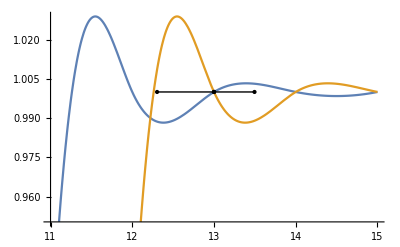

```mathematica
(* see *)
seePlot[p,2,{v1,v2},pyrf12[[m]]]
```

## Graphics for All pixels

### All Pixel Graphics

#### Test

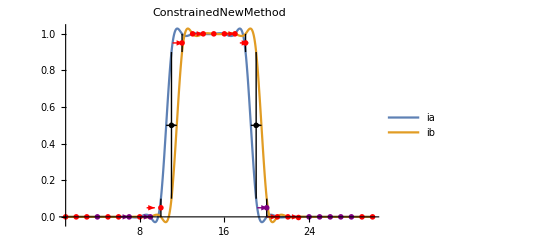

```mathematica
tes1=lineTest[Range[1,Length[line1]],pyrf12[[1;;4]],0.001,noteBookMode];
seeAllLine[Range[1,30],pyrf12[[1;;4]],0.001,noteBookMode]
```

## Graphics for One pixel

```mathematica
(* Function to find solutions for all levels of pyramid {l1,l2,l3,l4,...} or {l1} *)
(* Input-> {number of iterations, pixel of interests, pyrfunctions,threshold *)
(* Output-> {v1, v2,status}*)
PyrFlow1DIter[i_, p0_,v0_, pyrfunctions_,threshold_,"ConstrainedNewMethod"]:=Block[{c,updateValues,newVals,tableNewValues,iterTable,goodValIter},(

c=Length[pyrfunctions]; (* number of levels *)

(*{v1, v2, status, e}*)
updateValues={v0[[1]],v0[[2]],"ok",0};

Table[

(* compute at this scale, using current motion estimate *)
If[updateValues[[4]]<2,updateValues[[3]]="ok", updateValues={0.,0.,updateValues[[3]],2}];

(* we get 5 new values *)
(*Print[{Total[updateValues[[1;;2]]],updateValues[[1;;2]]}];*)
newVals=newValues[100,updateValues[[1;;2]]];

tableNewValues=Table[

updateValues[[1;;2]]=v;


iterTable=Table[

updateValues=PyrUpgrade1D[updateValues,p0, pyrfunctions[[-f]],threshold*2^(-c+1),"ConstrainedNewMethod"];
{updateValues[[1]], updateValues[[2]],updateValues[[3]]}
,{j,1,i}]

,{v,newVals}];

c=c-1;

goodValIter=pickNewValueIter[tableNewValues];
updateValues[[1;;2]]=Last[goodValIter][[1;;2]];

goodValIter
,{f,1,Length[pyrfunctions]}]

)];
```

```mathematica
pickNewValueIter[tableIterNewVals_]:=Block[{newIterVal},(

newIterVal=Select[tableIterNewVals,Last[#][[3]]==("converged")&,1];

If[newIterVal=={},
tableIterNewVals[[1]],
newIterVal[[1]]
]
)]
```

#### Test

```mathematica
Table[
PyrFlow1D[10, 11, pyrf12[[4;;4]],0.001,noteBookMode]==PyrFlow1DIter[10, 11,{0.,0.}, pyrf12[[4;;4]],0.001,noteBookMode][[-1,-1]]
,{p,1,30}]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

#### Test

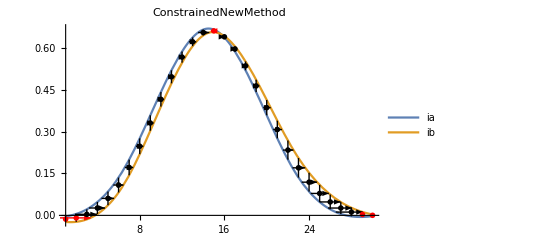

```mathematica
seeAllLine[Range[1,30],pyrf12[[4;;4]],0.001,noteBookMode]
```

```mathematica
lvlmin=4;
lvlmax=4;
p=14;
mode="ConstrainedNewMethod";
pixelInitialValueGraphics[10,2000,p,{-0,0},1, pyrf12[[lvlmin;;lvlmax]],0.001*2^(-lvlmin+1),mode]
```

$Aborted

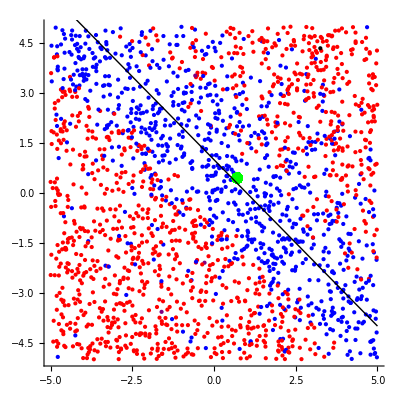

```mathematica
lvlmin=3;
lvlmax=3;
p=14;
mode="ConstrainedNewMethod";
pixelInitialValueGraphics[10,2000,p,{-5,5},1, pyrf12[[lvlmin;;lvlmax]],0.001*2^(-lvlmin+1),mode]
```